# Positivity scheme

## F2 NC DIS

### Gluon coefficient function

```mathematica
Pqgx[z_]:=2((1-z)^2 + z^2)
cgx[z_]:={-2+16z(1-z),Pqgx@z Log[(1-z)/z]}
```

```mathematica
Pqgmx[m_,z_]:=z^m *Pqgx@z
PqgLogOmXx[z_]:=Log[1-z]*Pqgx@z
```

```mathematica
cgN[n_]:=Evaluate@Integrate[z^(n-1)*cgx[z], {z,0,1}, Assumptions->Re[n]>0]
```

```mathematica
PqgmN[m_,n_]:=Evaluate@Integrate[z^(n-1)*Pqgmx[m,z], {z,0,1}, Assumptions->Re[n]>0]
PqgLogOmXN[n_]:=Evaluate@Integrate[z^(n-1)*PqgLogOmXx[z], {z,0,1}, Assumptions->Re[n]>0]
```

```mathematica
Series[cgN@n,{n,∞,1}]
```

{-2/n+O[1/n]^2,(-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2}

```mathematica
Series[PqgmN[m,n],{n,∞,1}]
Series[PqgLogOmXN[n],{n,∞,1}]
```

ConditionalExpression[2/(m+n)-4/(1+m+n)+4/(2+m+n),Re[m+n]>0]

(-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2

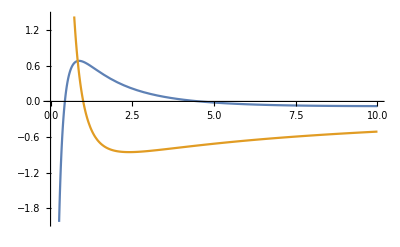

```mathematica
Plot[Evaluate@cgN@n, {n, 0, 10}]
```

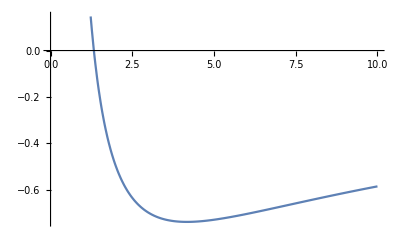

```mathematica
Plot[Plus@@cgN@n, {n, 0, 10}]
```

```mathematica
Series[Plus@@cgN@n - 2PqgLogOmXN[n],{n,∞,2}]
```

(2 (-1+EulerGamma+Log[n]))/n+(23-4 EulerGamma-4 Log[n])/n^2+O[1/n]^3

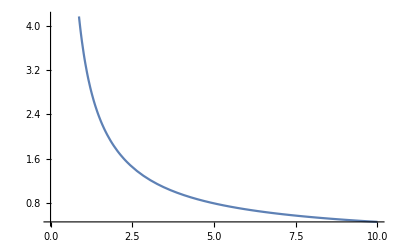

```mathematica
Plot[Plus@@cgN@n-2 PqgLogOmXN@n, {n, 0, 10}]
```

```mathematica
FullSimplify[(Plus@@cgN@n - PqgLogOmXN@n+PqgmN[0,n])>0,Assumptions->n>0]
```

True

#### Compare to Vogt et al.

```mathematica
s1[n_] := Evaluate@Sum[1/k, {k,1,n}]
s2[n_] := Evaluate@Sum[1/k^2, {k,1,n}]
s1c1[n_] := Evaluate@Sum[s1@k/k, {k,1,n}]
```

```mathematica
gqg[f_, n_] := 2f[n+2] - 4f[n+1] - f[n-1] + 3f[n]
```

```mathematica
vogtcg [n_] := -2 (gqg[s1c1 , n] + 4gqg[s1,n]-gqg[s2,n]) -6(s1[n-1] - s1[n])
```

```mathematica
FullSimplify[Vogtcg[n] - Plus@@cgN@n]
```

0

#### Compare with Altarelli

```mathematica
Altarellicg[n_] := -(s1[n-1]*(n^2 + n +2) / (n*(n+1)*(n+2)) + 1 /(n+2))
```

```mathematica
FullSimplify[(1/2) Vogtcg@n -Altarellicg@n]
```

```mathematica
4/(2+3 n+n^2)extension
```

```mathematica
Integrate[x^(n-1)4x(1-x), {x, 0, 1}]
```

ConditionalExpression[4/(2+3 n+n^2),Re[n]>-1]

```mathematica
AltarelliPqgN[n_]:=(n^2+n+2)/(n(n+1)(n+2))
```

```mathematica
FullSimplify[1/2PqgmN[0,n]- AltarelliPqgN@n]
```

ConditionalExpression[0,Re[n]>0]

### Quark coefficient function

```mathematica
cqRegx[z_]:=(6+4z)
cqDeltax=-(9+4Zeta[2]);
cqL1x[z_]:=-2(1+z)Log[(1-z)];
cqL0x[z_]:=2(1+z)Log[z] - 4 Log[z]/(1-z);
cqD0x[z_]:= -3/(1-z);
cqD1x[z_]:=4Log[1-z]/(1-z)
```

```mathematica
cqRegN[n_] := Evaluate@Integrate[cqRegx@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqDeltaN = cqDeltax;
cqL1N[n_] := Evaluate@Integrate[cqL1x@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqL0N[n_] := Evaluate@Integrate[cqL0x@z z^(n-1) ,{z,0,1}, Assumptions->Re[n]>0];
```

```mathematica
cqD0N[n_] := Evaluate@Integrate[cqD0x@z(z^(n-1)-1) ,{z,0,1}, Assumptions->Re[n]>0];
cqD1N[n_] := Evaluate@Integrate[cqD1x@z(z^(n-1)-1) ,{z,0,1}, Assumptions->Re[n]>0];
```

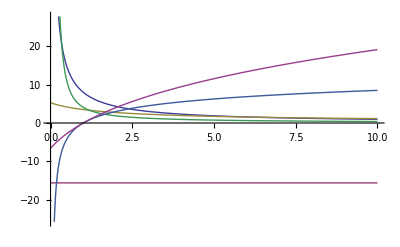

```mathematica
Plot[{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,0,10}]
```

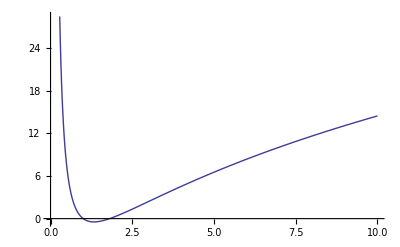

```mathematica
Plot[Plus@@{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,0,10}]
```

```mathematica
Series[{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}, {n,∞,1}]
```

{10/n+O[1/n]^2,-9-(2 π^2)/3,(4 EulerGamma-4 Log[1/n])/n+O[1/n]^2,4/n+O[1/n]^2,(3 EulerGamma-3 Log[1/n])-3/(2 n)+O[1/n]^2,(2 EulerGamma^2+π^2/3-4 EulerGamma Log[1/n]+2 Log[1/n]^2)+(-2-2 EulerGamma+2 Log[1/n])/n+O[1/n]^2}

```mathematica
PqqmN[m_,n_]:=Evaluate@Integrate[(2/(1-z))*(z^(n+m-1) - 1),{z, 0, 1}]
PqqLogOmXN[n_]:=Evaluate@Integrate[(2Log[1-z]/(1-z))*(z^(n-1) - 1),{z, 0, 1}]
```

#### Compare to Vogt et al.

```mathematica
gqq[f_, n_] := f[n+1] + f[n-1]
```

```mathematica
Vogtcq[n_] := 9(s1@n-1) +2(gqq[s1c1,n]+2gqq[s1,n]-gqq[s2,n])-7(s1[n-1]+s1[n])
```

```mathematica
FullSimplify[Vogtcq[n]-Plus@@{cqRegN@n,cqDeltax,cqL1N@n,cqL0N@n,cqD0N@n,cqD1N@n}]
```

0

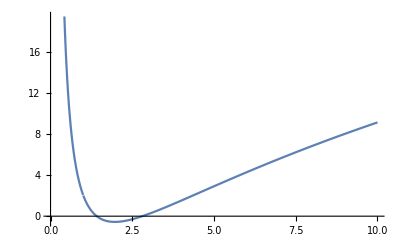

```mathematica
Plot[Vogtcq@n-PgqLogOmXN@n+PqqmN[0,n], {n, 0,10}]
```

```mathematica
Series[Vogtcq@n-PgqLogOmXN@n+PqqmN[0,n], {n, ∞,2}]
```

(-9+EulerGamma+2 EulerGamma^2-π^2/3+Log[n]+4 EulerGamma Log[n]+2 Log[n]^2)+(23/2+3 EulerGamma+3 Log[n])/n+(-37-16 EulerGamma-16 Log[n])/(12 n^2)+O[1/n]^3

#### Compare with Altarelli

```mathematica
Altarellicq[n_] := s1[n-1] (s1[n+1] + 3/2) + 4/n - 1/(n+1) -9/2 - s2[n-1]
```

```mathematica
FullSimplify[(1/2) Vogtcq@n -Altarellicq@n]
```

2/(1+n)

## Higgs production

### Gluon coefficient function

```mathematica
AltarelliQgg[n_] := 2(s1[n+2]^2 - 2s1[n+1]^2 + 3s1[n]^2-2s1[n-1]^2 + s1[n-2]^2)
```

```mathematica
Altarellichg[n_] := ((11 + 4 Pi^2)/3 - 22/(n(n^2-1)(n+2))) + 2AltarelliQgg@n
```

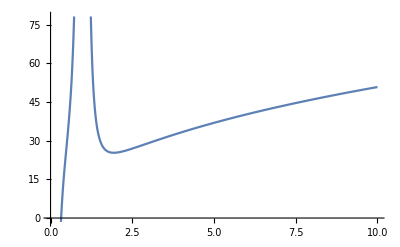

```mathematica
Plot[Altarellichg@n, {n, 0, 10}]
```

### Quark coefficient function

```mathematica
Pgqx[z_]:=((1-z)^2 + 1)/z
Pgqmx[m_,z_]:=z^m *Pgqx@z
PgqLogOmXx[z_]:=Log[1-z]*Pgqx@z
```

```mathematica
PgqmN[m_,n_]:=Evaluate@Integrate[z^(n-1)*Pgqmx[m,z], {z,0,1}, Assumptions->Re[n]>0]
PgqLogOmXN[n_]:=Evaluate@Integrate[z^(n-1)*PgqLogOmXx[z], {z,0,1}, Assumptions->Re[n]>0]
```

```mathematica
PgqLogOmXN@n
```

(2+3 n-(n (1+n) (2+n+n^2) (EulerGamma+PolyGamma[0,n]))/(-1+n))/(n^2 (1+n)^2)

```mathematica
AltarelliQgq[n_] := - 4 s1[n-1]/(n-1) + 4 s1[n]/n - 2s1[n+1]/(n+1) + 2/(n-1)^2 -2/n^2 +1/(n+1)^2
```

```mathematica
Altarellichq[n_] := (n^2-n-3)/(n(n^2-1)) + AltarelliQgq@n
```

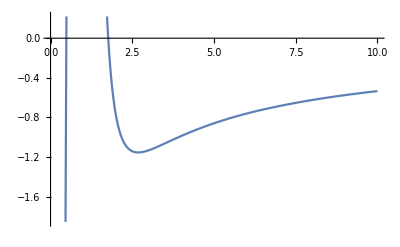

```mathematica
Plot[Altarellichq@n, {n, 0, 10}]
```

```mathematica
Series[Altarellichq@n, {n, ∞,1}]
```

(1/n+O[1/n]^3)+s1[n] (4/n+O[1/n]^3)+s1[-1+n] (-4/n-4/n^2+O[1/n]^3)+s1[1+n] (-2/n+2/n^2+O[1/n]^3)

```mathematica
Series[Altarellichq@n-4PgqLogOmXN@n, {n, ∞,2}]
```

(1+2 EulerGamma+2 Log[n])/n+(-1+2 EulerGamma+2 Log[n])/n^2+O[1/n]^3

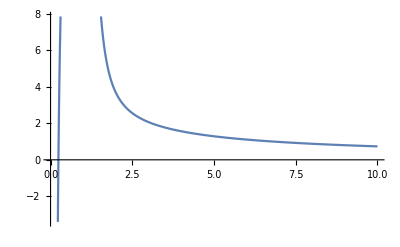

```mathematica
Plot[Altarellichq@n-4PgqLogOmXN@n, {n, 0,10}]
```

## Drell - Yan

### Quark-Gluon coefficient

```mathematica
Matsuuracqgx[z_] := (1 - 2z + 2z^2) Log [(1-z)^2/z] + (3 + 2z - 3z^2)/2
```

```mathematica
MatsuuracqgN[n_] = Integrate[z^(n-1) Matsuuracqgx@z, {z,0,1}, Assumptions->Re[n]>0]
```

ConditionalExpression[(4+n (18+n (30+n (18+n (5+n))))-2 n (1+n) (2+n) (2+n+n^2) HarmonicNumber[n])/(n^2 (1+n)^2 (2+n)^2),Re[n]>0]

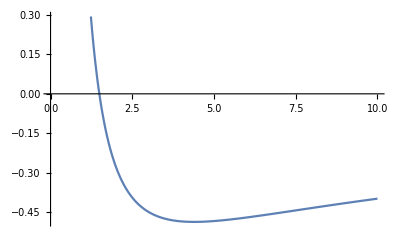

```mathematica
Plot[MatsuuracqgN@n, {n, 0, 10}]
```

```mathematica
Series[MatsuuracqgN@n, {n, ∞,1}]
```

(1-2 EulerGamma-2 Log[n])/n+O[1/n]^2

```mathematica
Series[MatsuuracqgN@n-2PgqLogOmXN@n+2 PgqmN[0,n], {n, ∞,2}]
```

3/n+(-1+6 EulerGamma+6 Log[n])/n^2+O[1/n]^3

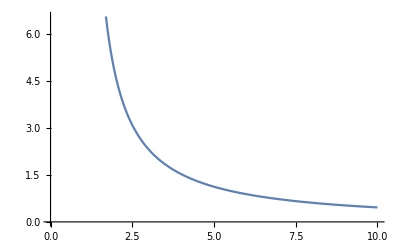

```mathematica
Plot[MatsuuracqgN@n-2PgqLogOmXN@n+2 PgqmN[0,n], {n, 0, 10}]
```

#### Quark - Quark coefficient

```mathematica
MatsuuracqqDeltax := 8 Zeta[2] - 16
MatsuuracqqD1x[z_] := 16 Log[1-z] /(1-z)
MatsuuracqqL1x[z_]  := - 8(1+z)Log[1-z]
MatsuuracqqL0x[z_]  := -4(1+z^2)/(1-z)Log[z]
```

```mathematica
MatsuuracqqDeltaN := MatsuuracqqDeltax
MatsuuracqqD1N[n_]  = Integrate[MatsuuracqqD1x@z (z^(n-1) - 1), {z,0,1}, Assumptions->Re[n]>0]
MatsuuracqqL1N[n_]  = Integrate[MatsuuracqqL1x@z  z^(n-1) , {z,0,1}, Assumptions->Re[n]>0]
MatsuuracqqL0N[n_]  = Integrate[MatsuuracqqL0x@z  z^(n-1) , {z,0,1}, Assumptions->Re[n]>0]
```

ConditionalExpression[4/3 (6 EulerGamma^2+π^2+6 PolyGamma[0,n] (2 EulerGamma+PolyGamma[0,n])-6 PolyGamma[1,n]),Re[n]>-1]

ConditionalExpression[(8 (n+(1+n) (1+2 n) HarmonicNumber[n]))/(n (1+n)^2),Re[n]>-1]

ConditionalExpression[-4/n^2-4/(1+n)^2+8 PolyGamma[1,n],Re[n]>0]

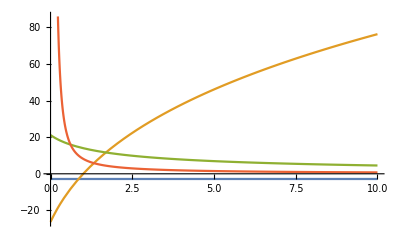

```mathematica
Plot[{MatsuuracqqDeltaN,MatsuuracqqD1N@n,MatsuuracqqL1N@n,MatsuuracqqL0N@n}, {n,0,10}]
```

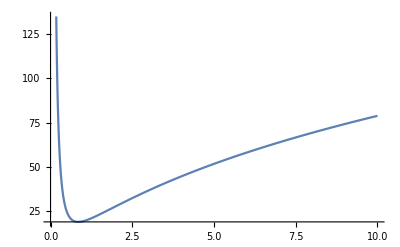

```mathematica
Plot[Plus@@{MatsuuracqqDeltaN,MatsuuracqqD1N@n,MatsuuracqqL1N@n,MatsuuracqqL0N@n}, {n,0,10}]
```